```mathematica
RalstonStep[f_,h_][{t0_,y0_}]:= Module[
{k1,k2,k3,z1,z2,z3},
k1=f[t0,y0];
z1 = y0+1/2 * k1*h; 
k2 = f[t0+1/2 h, z1];
z3= y0 + 3/4*k2*h;
k3=f[t0+3/4 h, z3];
{t0+h, y0 + h*(2/9 k1+1/3 k2 + 4/9 k3)}
]
```

Generate a “synthetic” ODE with a known solution

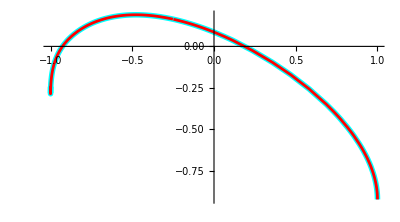

```mathematica
Clear[SynSol,ySol, f,t,y,g]
SynSol[t_]:= {Cos[t+Sin[t]], Sin[t] - Cos[Sin[t]-ArcTan[Cos[ t+ 2]+t]]}
f[t_,{y1_,y2_}]:={3.2 (y2+Sin[2 t]^2)Cos[t+y1], 2.3 t + Sin[t + y2]};
g[t_]= Simplify[ SynSol'[t]-f[t,SynSol[t]]];
{t0,y0}={0.0,SynSol[0.0]};
TMax=3.4;
ySol=NDSolveValue[ {y'[t]==f[t,y[t]]+g[t],y[t0]==y0},y,{t,t0, TMax}];
ParametricPlot[{ySol[t],SynSol[t]},{t, 0, TMax},
PlotStyle->{{Cyan, Thickness[0.01]},{Red,Thickness[0.005]}}]
```

```mathematica
RalstonStep[f,h]
```

RalstonStep[f,h]

```mathematica
LogLogPlot[RalstonStep[]]
```

```mathematica
NDSolveValue[ {y'[t]==f[t,y]+g[t],y[t0]==y0},y,{t,0, TMax}]
```

SetDelayed::write: Tag NDSolveValue in NDSolveValue[{y'[t]==3.2 Cos[y[t]] (1+Sin[«1»]^2)-3.2 Cos[y[t][t]] (1+Sin[«1»]^2)+NDSolveValue[(«1»)^(«1»)[«1»]=={«2»},y[«1»]=={«2»}]'[t],y[0.]==NDSolveValue[y'[t]=={Times[«3»]+Times[«3»]+Times[«3»],«1»},y[0]=={«1»}][0.]},y,{«1»}][t_] is Protected.

$Failed

3.2 Cos[y[t]] (1+Sin[2 t]^2)

-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+NDSolveValue[{y'[t]==3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+NDSolveValue[y'[t]=={3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)-(1+Cos[t]) Sin[t+Sin[t]],Cos[t]+3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+(-Cos[t]+(1-Sin[2+t])/(1+(t+Cos[2+t])^2)) Sin[ArcTan[t+Cos[2+t]]-Sin[t]]},y[0]=={1.,-0.923247}]'[t],y[0.]==NDSolveValue[y'[t]=={3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)-(1+Cos[t]) Sin[t+Sin[t]],Cos[t]+3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+(-Cos[t]+(1-Sin[2+t])/(1+(t+Cos[2+t])^2)) Sin[ArcTan[t+Cos[2+t]]-Sin[t]]},y[0]=={1.,-0.923247}][0.]},y,{t,0,3.2}]'[t]

{0.,NDSolveValue[{y'[t]==3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+NDSolveValue[y'[t]=={3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)-(1+Cos[t]) Sin[t+Sin[t]],Cos[t]+3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+(-Cos[t]+(1-Sin[2+t])/(1+(t+Cos[2+t])^2)) Sin[ArcTan[t+Cos[2+t]]-Sin[t]]},y[0]=={1.,-0.923247}]'[t],y[0.]==NDSolveValue[y'[t]=={3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)-(1+Cos[t]) Sin[t+Sin[t]],Cos[t]+3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+(-Cos[t]+(1-Sin[2+t])/(1+(t+Cos[2+t])^2)) Sin[ArcTan[t+Cos[2+t]]-Sin[t]]},y[0]=={1.,-0.923247}][0.]},y,{t,0,3.2}][0.]}

NDSolveValue::argm: NDSolveValue called with 2 arguments; 3 or more arguments are expected.

General::stop: Further output of NDSolveValue::argm will be suppressed during this calculation.

NDSolveValue::litarg: To avoid possible ambiguity, the arguments of the dependent variable in NDSolveValue[y'[t]=={3.2 Cos[y[t]] (1+Sin[«1»]^2)-3.2 Cos[y[t][t]] (1+Sin[«1»]^2)-(1+Cos[t]) Sin[t+Sin[«1»]],Cos[t]+3.2 Cos[y[t]] (1+Sin[«1»]^2)-«1»+(-Cos[«1»]+Power[«2»] Plus[«2»]) Sin[ArcTan[«1»]+Times[«2»]]},y[0]==«1»] should literally match the independent variables.

NDSolveValue::litarg: To avoid possible ambiguity, the arguments of the dependent variable in «1» should literally match the independent variables.

General::stop: Further output of NDSolveValue::litarg will be suppressed during this calculation.

NDSolveValue[{y'[t]==3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+NDSolveValue[{y'[t]==3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+NDSolveValue[y'[t]=={3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)-(1+Cos[t]) Sin[t+Sin[t]],Cos[t]+3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+(-Cos[t]+(1-Sin[2+t])/(1+(t+Cos[2+t])^2)) Sin[ArcTan[t+Cos[2+t]]-Sin[t]]},y[0]=={1.,-0.923247}]'[t],y[0.]==NDSolveValue[y'[t]=={3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)-(1+Cos[t]) Sin[t+Sin[t]],Cos[t]+3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+(-Cos[t]+(1-Sin[2+t])/(1+(t+Cos[2+t])^2)) Sin[ArcTan[t+Cos[2+t]]-Sin[t]]},y[0]=={1.,-0.923247}][0.]},y,{t,0,3.2}]'[t],y[0.]==NDSolveValue[{y'[t]==3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+NDSolveValue[y'[t]=={3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)-(1+Cos[t]) Sin[t+Sin[t]],Cos[t]+3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+(-Cos[t]+(1-Sin[2+t])/(1+(t+Cos[2+t])^2)) Sin[ArcTan[t+Cos[2+t]]-Sin[t]]},y[0]=={1.,-0.923247}]'[t],y[0.]==NDSolveValue[y'[t]=={3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)-(1+Cos[t]) Sin[t+Sin[t]],Cos[t]+3.2 Cos[y[t]] (1+Sin[2 t]^2)-3.2 Cos[y[t][t]] (1+Sin[2 t]^2)+(-Cos[t]+(1-Sin[2+t])/(1+(t+Cos[2+t])^2)) Sin[ArcTan[t+Cos[2+t]]-Sin[t]]},y[0]=={1.,-0.923247}][0.]},y,{t,0,3.2}][0.]},y,{t,0,3.2}]

```mathematica
f[t_,
TMax=3.2;ParametricPlot[ySol[t],{t, 0, TMax}]
```

{-3.2 Cos[y[t]] (1+Sin[2 t]^2)-(1+Cos[t]) Sin[t+Sin[t]],Cos[t]-3.2 Cos[y[t]] (1+Sin[2 t]^2)+(-Cos[t]+(1-Sin[2+t])/(1+(t+Cos[2+t])^2)) Sin[ArcTan[t+Cos[2+t]]-Sin[t]]}

```mathematica
Roseler[
{t0,y0}={0.0, {1.2,3.4,5.6}};
NestList
```